```mathematica
Get[NotebookDirectory[]<>"BSFfast.m"]
```

```mathematica
BSFfastFunctionNames
```

{Private`BSFfastσvtopPlat,Private`BSFfastσvtopCut,Private`BSFfastσvbotPlat,Private`BSFfastσvbotCut,Private`BSFfastσvnoTPlat,Private`BSFfastσvnoTCut,Private`BSFfastσvdqedConst,Private`BSFfastσvdqedNoTConst,Private`BSFfastσvqcdNoTConst,Private`BSFfastσvtopPlatF,Private`BSFfastσvtopCutF,Private`BSFfastσvbotPlatF,Private`BSFfastσvbotCutF,Private`BSFfastσvnoTPlatF,Private`BSFfastσvnoTCutF,Private`BSFfastσvdqedConstF,Private`BSFfastσvdqedNoTConstF,Private`BSFfastσvqcdNoTConstF Private`BSFfastσvqedInclTopF,Private`BSFfastσvqedExclTopF}

```mathematica
?BSFfastSigmavEffBSF
```

(*SM-QCD models: {"QCD-SU","QCD-FU","QCD-SD","QCD-FD","QCD-S","QCD-F"}*)
	(* → αs: {"Cut","Plat"}*)
(*dQCD/dQED models: {"dQCD-S","dQCD-F","dQED-S","dQED-F","dQED-S_nT","dQED-F_nT"}*)
	(* → α some number. (UVi warnings yet to be implemented)*)
(*SM-QED models: {“QED-S”,”QED-F”,”QED-F_noTop}*)
	(*→ “QED-F” includes BS-decay via s-channel photons into SM fermions. Top-Antitop pairs can be excluded but are negligible*)

```mathematica
BSFfastSigmavEffBSF["QCD-FU","Cut"][10^7.,12345.6]//AbsoluteTiming
```

{0.000096,5.07632×10^-15}

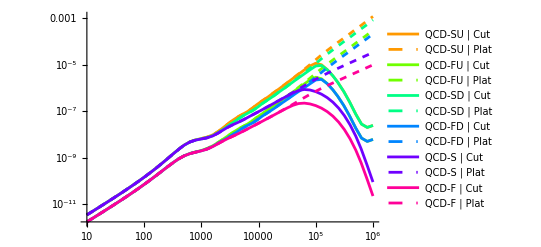

```mathematica
fn=Join@@Table[Legended[BSFfastSigmavEffBSF[model,as][10^4.,x],model<>" | "<>as],{model,{"QCD-SU","QCD-FU","QCD-SD","QCD-FD","QCD-S","QCD-F"}},{as,{"Cut","Plat"}}]//Evaluate;
LogLogPlot[fn,{x,10,10^6},PlotStyle->Flatten[{{Bold,#},{Dashed,#}}&/@Hue/@Range[.1,.9,.8/5],1]]
```

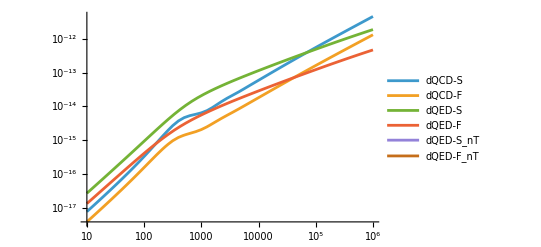

```mathematica
fnresc=Table[Legended[BSFfastSigmavEffBSF[model,0.1][10^7.,x],model],{model,{"dQCD-S","dQCD-F","dQED-S","dQED-F","dQED-S_nT","dQED-F_nT"}}]//Evaluate;
LogLogPlot[fnresc,{x,10,10^6}]
```

```mathematica
BSFfastSigmavEffBSF["QED-F"]==BSFfastSigmavEffBSF["QED-F",1/128.9]
```

True

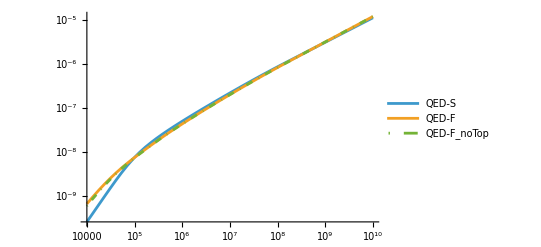

```mathematica
fnSMqed=Table[Legended[BSFfastSigmavEffBSF[model][10^3.,x],model],{model,{"QED-S","QED-F","QED-F_noTop"}}]//Evaluate;
LogLogPlot[fnSMqed,{x,10^4,10^10},PlotStyle->{Bold,Bold,DotDashed}]
```